```mathematica
Exit[]
```

# NNLO approximation

Here we test that the methodology is able to recover the known NNLO singles splitting functions given the same inputs.

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]

(* N space expression from pegasus *)
Get[StringJoin[here, "g2_singlet.m"]]
Get[StringJoin[here, "qcd_cusp.m"]]

LaunchKernels[4];
```

```mathematica
PlotRelativeDiffMoments[fexa_, ffitted_, nflav_, Nmin_, Nmax_] := Module[{difflist, nmax, ffitednum, fexanum},
   	(* N space relative difference plot *)
   	ffitednum = ffitted //. QCDConstantsRules /. ZetaRules;
   	fexanum = fexa /. N -> n //. NF-> nf //. HarmonicNumber[a_,b_] -> S[b, a] //.  HarmonicNumber[a_] -> S[1, a] //. QCDConstantsRules /. ZetaRules;
   	difflist = Table[(ffitednum - fexanum)/fexanum *100 //. nf -> nflav, {n, Nmin, Nmax}];
   	ListPlot[MapThread[{#1, #2} &, {Range[Nmin, Nmax], difflist}], PlotLabel -> StringForm["% difference (fitted-exact)/exact, NF=``", nflav], ImageSize -> Medium]
];

PlotRelativeDiffNf[fexa_, ffitted_, nflav_, Nmin_, Nmax_] := Module[{difflist, nmax, ffitednum, fexanum},
   	(* N space relative difference plot *)
   	ffitednum = Coefficient[ffitted //. QCDConstantsRules /. ZetaRules, nf, nflav];
   	fexanum = Coefficient[fexa /. N -> n //. NF-> nf //. HarmonicNumber[a_,b_] -> S[b, a] //.  HarmonicNumber[a_] -> S[1, a] //. QCDConstantsRules /. ZetaRules, nf,nflav];
   	difflist = Table[(ffitednum - fexanum)/fexanum *100, {n, Nmin, Nmax}];
   	ListPlot[MapThread[{#1, #2} &, {Range[Nmin, Nmax], difflist}], PlotLabel -> StringForm["% difference (fitted-exact)/exact, NF^``", nflav], ImageSize -> Medium]
];

pifact =  (0.2/(4 Pi))^3 x;
```

### Gamma gg

#### Build limits

```mathematica
Nfmin = 0;
Nfmax = 2;
gggmoments = MapThread[P2GGN /. N -> # /. NF -> nf &, {Range[2,8,2]}];
(* ggg2Ninf = - QCDcusp3 4^3 S[1,n] /. GluonConstants //. QCDConstantsRules; *)
ggg2Ninf =  (Series[P2GGN /. N -> n /. NF -> nf, {n, Infinity,0}] // Normal) /. Log[n] -> S[1,n] - EulerGamma //Expand;
ggg2N0asy = Series[P2GGN /. N -> n /. NF -> nf, {n, 0,-3}] // Normal;
ggg2N1asy = Series[P2GGN /. N -> n /. NF -> nf, {n, 1,-2}] // Normal;
```

#### Fits

```mathematica
(* Small N based paramtization *)
FitBasis1 = {
    {1/(n-1), 1/n, 1/n^2, Lm11[n]},
	{1/(n-1), 1/n, 1/n^2, Lm11[n]},
	{1/(n-1), 1/n, 1/n^2, Lm11[n]}
};
ggg2Fitted1 = AdFitSinglet[gggmoments,Nfmin, Nfmax, ggg2N0asy,ggg2N1asy, ggg2Ninf, FitBasis1];

(* Inermediate case *)
 FitBasis2 = {
	{1/(n-1), Lm13m1[n], 1/(n), Lm11[n]},
	{1/(n-1), Lm13m1[n], 1/(n), Lm11[n]},
	{1/(n-1), Lm13m1[n], 1/(n), Lm11[n]}
};
ggg2Fitted2 = AdFitSinglet[gggmoments,Nfmin, Nfmax, ggg2N0asy,ggg2N1asy, ggg2Ninf, FitBasis2];

(* Large N based paramertrization  *)
 FitBasis3 = {
	 {1/(n-1), 1, 1/(n+1)^2, Lm11[n]},
	{1/(n-1), 1, 1/(n+1)^2, Lm11[n]},
	{1/(n-1), 1, 1/(n+1)^2, Lm11[n]}
};	
ggg2Fitted3 = AdFitSinglet[gggmoments,Nfmin, Nfmax, ggg2N0asy,ggg2N1asy, ggg2Ninf, FitBasis3];

(* Best fit *)
FitBasisTest = {
    {1/(n-1), 1/(n+1), 1/n^2, Lm11[n]},
	{1/(n-1), 1/(n+1), 1/n^2, Lm11[n]},
	{1/(n-1), 1/(n+1), 1/n^2, Lm11[n]}
};
ggg2FittedTest = AdFitSinglet[gggmoments,Nfmin, Nfmax, ggg2N0asy,ggg2N1asy, ggg2Ninf, FitBasisTest];
```

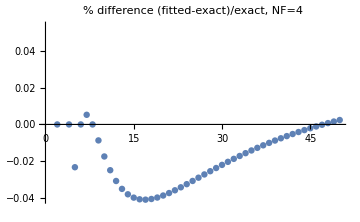

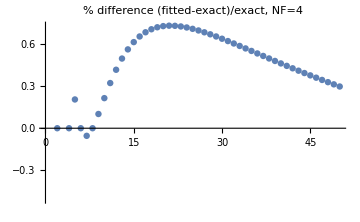

```mathematica
(* Compare to full experssion *)
PlotRelativeDiffMoments[P2GGN, ggg2Fitted1 + ggg2N0asy + ggg2N1asy + ggg2Ninf, 4, 2, 50]
PlotRelativeDiffMoments[P2GGN, ggg2Fitted3 + ggg2N0asy + ggg2N1asy + ggg2Ninf, 4, 2, 50]
```

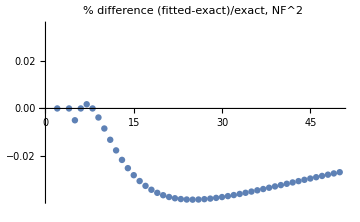

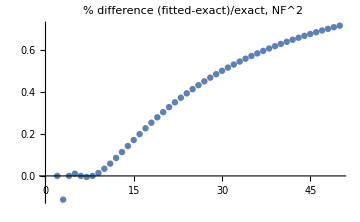

```mathematica
(* Compare to nf^2 *)
PlotRelativeDiffNf[P2GGN, ggg2Fitted1 + ggg2N0asy + ggg2N1asy+ ggg2Ninf, 2, 2, 50]
PlotRelativeDiffNf[P2GGN, ggg2Fitted3 + ggg2N0asy + ggg2N1asy+ ggg2Ninf, 2, 2, 50]
```

#### Plots

```mathematica
PlotXspaceSinglet["P_gg^(2)(x) nf=4, series in α_s", ggg2Fitted1, ggg2N0asy, ggg2N1asy, ggg2Ninf, 4, 0.000001, 0.0001]
PlotXspaceSinglet["P_gg^(2)(x) nf=4, series in α_s", ggg2Fitted2, ggg2N0asy, ggg2N1asy, ggg2Ninf, 4, 0.000001, 0.0001]
PlotXspaceSinglet["P_gg^(2)(x) nf=4, series in α_s", ggg2Fitted3, ggg2N0asy, ggg2N1asy, ggg2Ninf, 4, 0.000001, 0.0001]
```

Limit for x=1 : -0.0197787+0.0387536/(-1+x)-0.0606188 x-0.102412 Log[1-x]

-Graphics-

Limit for x=1 : -0.150447+0.0387536/(-1+x)+0.379624 x-0.110107 Log[1-x]+0.263666 Log[1-x]^3-0.263666 x Log[1-x]^3

-Graphics-

Limit for x=1 : 0.814769+0.0387536/(-1+x)-1.26396 x-0.203024 Log[1-x]

-Graphics-

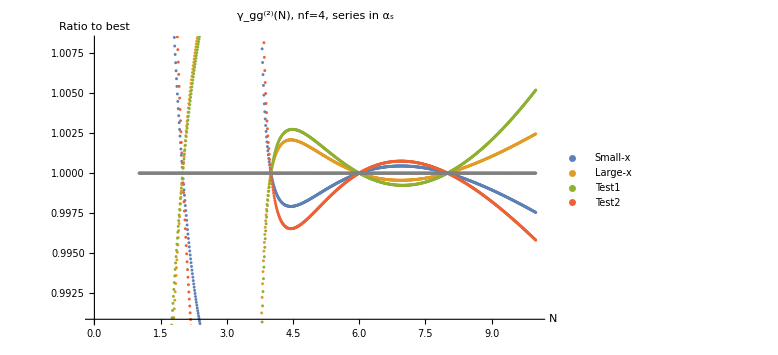

```mathematica
PlotRatioToBest[ggg2Fitted1, ggg2Fitted3, ggg2Fitted2, ggg2FittedTest, 4, "γ_gg^(2)(N), nf=4, series in α_s" ]
```

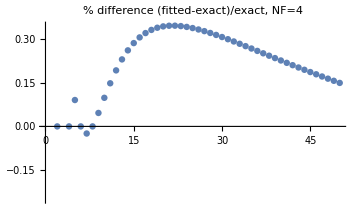

Limit for x=1 : 0.397495+0.0387536/(-1+x)-0.662288 x-0.152718 Log[1-x]

-Graphics-

```mathematica
ggg2FittedRef = (ggg2Fitted1 + ggg2Fitted3)/2;
PlotRelativeDiffMoments[P2GGN /. N -> n //. NF-> nf //. HarmonicNumber[a_,b_] -> S[b, a] //.  HarmonicNumber[a_] -> S[1, a], ggg2FittedRef + ggg2N0asy + ggg2N1asy+ ggg2Ninf, 4, 2, 50]
PlotXspaceSinglet["P_gg^(2)(x) nf=4, series in α_s", ggg2FittedRef, ggg2N0asy, ggg2N1asy, ggg2Ninf, 4, 0.000001, 0.0001]
```

#### Save

```mathematica
exportMe[ggg2N0asy + ggg2N1asy + ggg2Ninf, ggg2Fitted1, ggg2Fitted3, StringJoin[path, "ggg2nf0.c"], 0];
exportMe[ggg2N0asy + ggg2N1asy + ggg2Ninf, ggg2Fitted1, ggg2Fitted3, StringJoin[path, "ggg2nf1.c"], 1];
exportMe[ggg2N0asy + ggg2N1asy + ggg2Ninf, ggg2Fitted1, ggg2Fitted3, StringJoin[path, "ggg2nf2.c"], 2];
```

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggg2nf0.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggg2nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggg2nf2.c

#### Replica fits

```mathematica
thrhigh = 10^-7;
thrlow = 10^-3;
fsmallN = {1/(n-1), 1/(n-1), 1/(n-1)};
flargeN = {Lm11[n],Lm11[n],Lm11[n]};
fSubLeadingtot = {
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2},
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{S12m2[n],S12m2[n],S12m2[n]},
	{Lm11m1[n],Lm11m1[n],Lm11m1[n]},
	{S11m2[n],S11m2[n],S11m2[n]},
	{1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n}
};
ggg2asy = MellinInverseSinglet[ggg2N0asy + ggg2N1asy + ggg2Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
ggg2analyticN = P2GGN /. N -> n //. NF-> nf //. HarmonicNumber[a_,b_] -> S[b, a] //.  HarmonicNumber[a_] -> S[1, a] //. QCDConstantsRules /. ZetaRules;
ggg2analyticX = MellinInverseSinglet[ggg2analyticN] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
```

Part::partw: Part 2 of #1 does not exist.

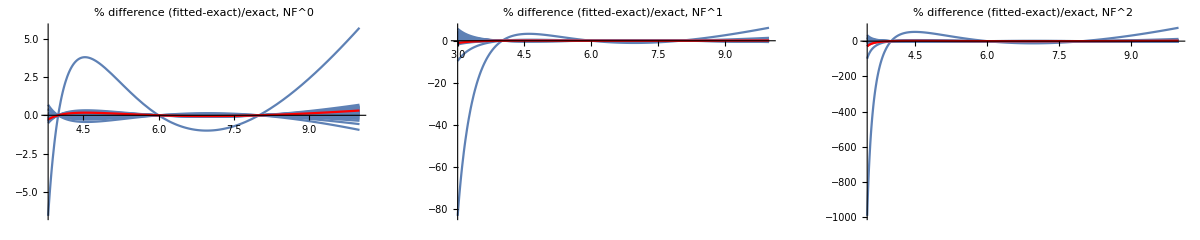

Smooth candidates: 31 out of 36

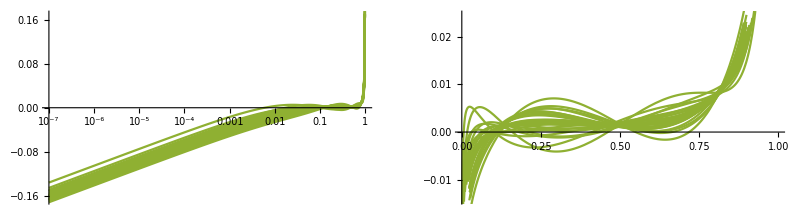

```mathematica
ggg2FittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, gggmoments, ggg2N0asy, ggg2N1asy, ggg2Ninf,True];
GraphicsRow[{
	PlotRelativeDiffIterate[Coefficient[ggg2analyticN  - (ggg2N0asy + ggg2N1asy + ggg2Ninf),nf,0],ggg2FittedCross,0,3.8,10],
	PlotRelativeDiffIterate[Coefficient[ggg2analyticN  - (ggg2N0asy + ggg2N1asy + ggg2Ninf),nf,1],ggg2FittedCross,1,3,10],
	PlotRelativeDiffIterate[Coefficient[ggg2analyticN  - (ggg2N0asy + ggg2N1asy + ggg2Ninf),nf,2],ggg2FittedCross,2,3.5,10]
}, ImageSize->Full]
ggg2invfull = ListMellinInverse[ggg2FittedCross];
ggg2inv = SelectSmoothCandidates[ggg2invfull, 4,thrlow,thrlow];
graphGGrep = PlotList[ggg2inv, ggg2asy, 4, 3] // Show;
graphGGlogrep = LogPlotList[ggg2inv, ggg2asy, 4, 3] // Show;
GraphicsRow[{graphGGlogrep,graphGGrep}]
```

```mathematica
ggg2cherry = SelectCherries[ggg2FittedCross, {1/n, 1/n^2}];
```

Selected cherries are: 15 out of 36

```mathematica
{graphGGcherry, graphGGcherrylog} = PlotErrorBand[ggg2asy,ggg2cherry,4,1];
{graphGG, graphGGlog} = PlotErrorBand[ggg2asy,ggg2inv,4,2];
graphGGExa = Plot[pifact ggg2analyticX /. nf -> 4, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphGGExalog = LogLinearPlot[ pifact ggg2analyticX /. nf -> 4, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
legend ={"all candidates","cherry-picked","analytic"};
GraphicsRow[{
	ShowLegends[{graphGGlog, graphGGcherrylog, graphGGExalog}, LogLinearPlot, legend, {2,1,4}], 
	ShowLegends[{graphGG, graphGGcherry, graphGGExa}, Plot, legend, {2,1,4}] 
	}, ImageSize -> Full
]
```

-Graphics-

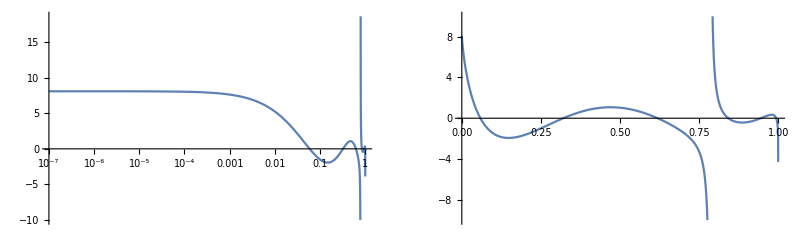

```mathematica
(* Relative difference *)
avgtot = Mean[ggg2cherry];
reldiff = (avgtot - ggg2analyticX + ggg2asy) /(ggg2analyticX - ggg2asy) * 100 /. nf -> 4;
r1 = Plot[reldiff, {x, 0, 1}, PlotRange->{All, {-10, 10}}];
r2 = LogLinearPlot[reldiff, {x, 10^-7, 1}];
GraphicsRow[{r2,r1}]
```

### Gamma gq

#### Build limits

```mathematica
Nfmin = 0;
Nfmax = 2;
ggqmoments = MapThread[P2GQN /. N -> # /. NF -> nf &, {Range[2, 8, 2]}];
ggq2Ninf =  (Series[P2GQN /. N -> n /. NF -> nf, {n, Infinity, 0}] // Normal ) /. Log[n] -> S[1, n] - EulerGamma  // Expand;
ggq2N0asy = Series[P2GQN /. N -> n /. NF -> nf, {n, 0, -3}] // Normal;
ggq2N1asy = Series[P2GQN /. N -> n /. NF -> nf, {n, 1, -2}] // Normal;
```

Series::ztest1: Unable to decide whether numeric quantity -1/2 PolyGamma[2,1]-Zeta[3] is equal to zero. Assuming it is.

Test how the LL aproximation of gq = cf/ca gg is violated at NNLO.

```mathematica
a1 = Coefficient[Series[P2GGN, {N, 1, 0}] cf/ca /. QCDConstantsRules // Normal , (N - 1), -2] // Simplify
a2 = Coefficient[Series[P2GQN, {N, 1, 0}] /. QCDConstantsRules // Normal , (N - 1), -2]
CoefficientList[a1,NF] / CoefficientList[a2,NF]
a1 = Coefficient[Series[P2GGN, {N, 1, 0}] cf/ca /. QCDConstantsRules // Normal , (N - 1), -1] // Simplify
a2 = Coefficient[Series[P2GQN, {N, 1, 0}] /. QCDConstantsRules // Normal , (N - 1), -1] // Simplify
CoefficientList[a1,NF] / CoefficientList[a2,NF]
```

-1189.24-69.8978 NF

-1189.3-71.082 NF

{0.999953,0.98334}

6317.33+81.3156 NF-1.24371 NF^2

6163.1+(-46.41-2.37037 NF) NF

{1.02503,-1.75211,0.524691}

#### Fits

```mathematica
(* Small-N parametrization *)
FitBasis1 = {
   	{Lm13[n], 1/(n-1), 1/n^2, 1/n},
   	{Lm13[n], 1/(n-1), 1/n^2, 1/n},
   	{Lm13[n], 1/(n-1), 1/n^2, 1/n}
   };
ggq2Fitted1 = AdFitSinglet[ggqmoments, Nfmin, Nfmax, ggq2N0asy, ggq2N1asy, ggq2Ninf, FitBasis1];

(* Intermediate case *)
FitBasis2 = {
   	{Lm14[n], 1/(n-1), (n+1)/(n)^2, Lm11[n]},
   	{Lm14[n], 1/(n-1), (n+1)/(n)^2, Lm11[n]},
   	{Lm14[n], 1/(n-1), (n+1)/(n)^2, Lm11[n]}
   };
ggq2Fitted2 = AdFitSinglet[ggqmoments, Nfmin, Nfmax, ggq2N0asy, ggq2N1asy, ggq2Ninf, FitBasis2];

(* Large-N parametrization *)
FitBasis3 = {
   	{Lm13[n], 1/(n-1), (n+1)/(n)^2, Lm12[n]},
   	{Lm13[n], 1/(n-1), (n+1)/(n)^2, Lm12[n]},
   	{Lm13[n], 1/(n-1), (n+1)/(n)^2, Lm12[n]}
   };
ggq2Fitted3 = AdFitSinglet[ggqmoments, Nfmin, Nfmax, ggq2N0asy, ggq2N1asy, ggq2Ninf, FitBasis3];

(* overfit *)
FitBasisTest = {
   	{Lm14[n], 1/(n-1), 1/(n+1), 1/(n), 1/(n)^2},
   	{Lm14[n], 1/(n-1), 1/(n+1), 1/(n), 1/(n)^2},
   	{Lm14[n], 1/(n-1), 1/(n+1), 1/(n), 1/(n)^2}
   };
ggq2FittedTest = AdFitSinglet[ggqmoments, Nfmin, Nfmax, ggq2N0asy, ggq2N1asy, ggq2Ninf, FitBasisTest];
```

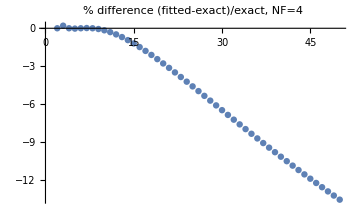

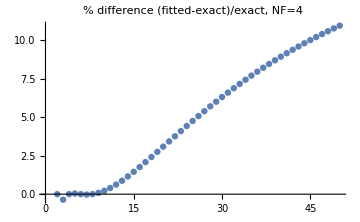

```mathematica
PlotRelativeDiffMoments[P2GQN, ggq2Fitted1 + ggq2N0asy + ggq2N1asy + ggq2Ninf, 4, 2, 50]
PlotRelativeDiffMoments[P2GQN, ggq2Fitted3 + ggq2N0asy + ggq2N1asy + ggq2Ninf, 4, 2, 50]
```

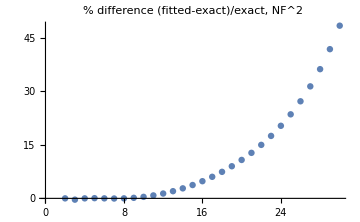

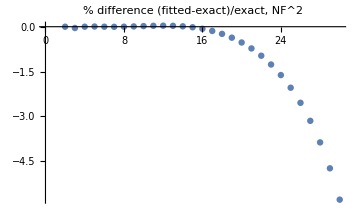

```mathematica
PlotRelativeDiffNf[P2GQN, ggq2Fitted1 + ggq2N0asy + ggq2N1asy + ggq2Ninf, 2, 2, 30]
PlotRelativeDiffNf[P2GQN, ggq2Fitted3 + ggq2N0asy + ggq2N1asy + ggq2Ninf, 2, 2, 30]
```

#### Plots

```mathematica
PlotXspaceSinglet["P_gq^(2)(x) nf=4, series in α_s", ggq2Fitted1, ggq2N0asy, ggq2N1asy, ggq2Ninf, 4, 0.000001, 0.0001]
PlotXspaceSinglet["P_gq^(2)(x) nf=4, series in α_s", ggq2Fitted2, ggq2N0asy, ggq2N1asy, ggq2Ninf, 4, 0.000001, 0.0001]
PlotXspaceSinglet["P_gq^(2)(x) nf=4, series in α_s", ggq2Fitted3, ggq2N0asy, ggq2N1asy, ggq2Ninf, 4, 0.000001, 0.0001]
```

Limit for x=1 : -0.016526-0.00397232 x+0.00010754 Log[1-x]^3

-Graphics-

Limit for x=1 : -0.013658-0.0227184 x-0.00667776 Log[1-x]-0.0000512333 Log[1-x]^4

-Graphics-

Limit for x=1 : -0.00972336-0.0246857 x+0.00441732 Log[1-x]^2+0.000907979 Log[1-x]^3

-Graphics-

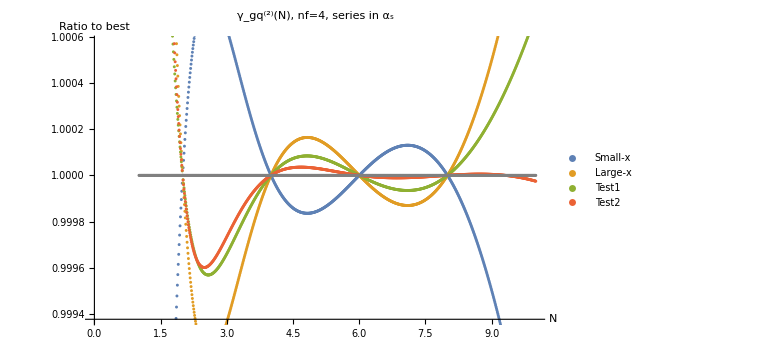

```mathematica
PlotRatioToBest[ggq2Fitted1, ggq2Fitted3, ggq2Fitted2, ggq2FittedTest, 4, "γ_gq^(2)(N), nf=4, series in α_s" ]
```

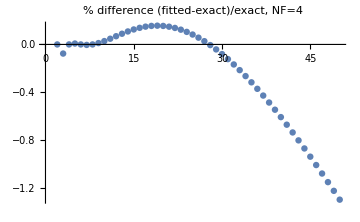

Limit for x=1 : -0.0131247-0.014329 x+0.00220866 Log[1-x]^2+0.00050776 Log[1-x]^3

-Graphics-

```mathematica
ggq2FittedRef = (ggq2Fitted1 + ggq2Fitted3)/2;
PlotRelativeDiffMoments[P2GQN /. N -> n //. NF-> nf //. HarmonicNumber[a_,b_] -> S[b, a] //.  HarmonicNumber[a_] -> S[1, a], ggq2FittedRef + ggq2N0asy + ggq2N1asy+ ggq2Ninf, 4, 2, 50]
PlotXspaceSinglet["P_gq^(2)(x) nf=4, series in α_s", ggq2FittedRef, ggq2N0asy, ggq2N1asy, ggq2Ninf, 4, 0.000001, 0.0001]
```

#### Save

```mathematica
exportMe[ggq2N0asy + ggq2N1asy + ggq2Ninf, ggq2Fitted1, ggq2Fitted3, StringJoin[path, "ggq2nf0.c"], 0];
exportMe[ggq2N0asy + ggq2N1asy + ggq2Ninf, ggq2Fitted1, ggq2Fitted3, StringJoin[path, "ggq2nf1.c"], 1];
exportMe[ggq2N0asy + ggq2N1asy + ggq2Ninf, ggq2Fitted1, ggq2Fitted3, StringJoin[path, "ggq2nf2.c"], 2];
```

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggq2nf0.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggq2nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggq2nf2.c

#### Replica fits

```mathematica
thrhigh = 10^-7;
thrlow = 10^-3;
fsmallN = {1/(n-1), 1/(n-1), 1/(n-1)};
flargeN = {S13m1[n],S13m1[n],S13m1[n]};
fSubLeadingtot = {
	{1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2)},
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{S12m1[n],S12m1[n],S12m1[n]},
	{Lm13[n],Lm13[n],Lm13[n]},
	{Lm12[n],Lm12[n],Lm12[n]},
	{Lm11[n],Lm11[n],Lm11[n]}, 
	{1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n}
};
```

```mathematica
ggq2asy = MellinInverseSinglet[ggq2N0asy + ggq2N1asy + ggq2Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
ggq2analyticN = ReduceToBasis[P2GQN] /. N -> n //. NF -> nf //. HarmonicNumber[a_, b_] -> S[b, a] //.  HarmonicNumber[a_] -> S[1, a] //. QCDConstantsRules /. ZetaRules;
ggq2analyticX = (InvMellin[ReduceToBasis[ggq2analyticN] /. n -> n + 1, n, x] /. InvMellinRules  /. LimitRules /. ZetaRules  ) /. Delta[__] -> 0 /. hrep // Simplify //Chop;
```

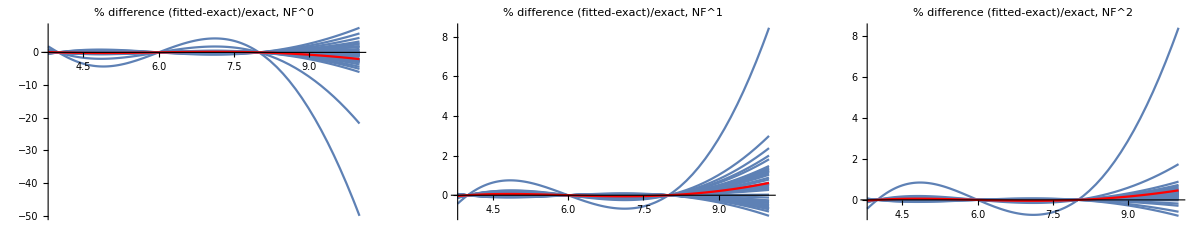

Smooth candidates: 43 out of 45

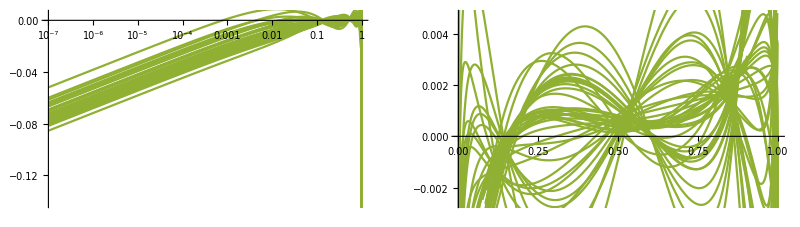

```mathematica
ggq2FittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, ggqmoments, ggq2N0asy, ggq2N1asy, ggq2Ninf,True];
GraphicsRow[{
	PlotRelativeDiffIterate[Coefficient[ggq2analyticN  - (ggq2N0asy + ggq2N1asy + ggq2Ninf),nf,0],ggq2FittedCross,0,3.8,10],
	PlotRelativeDiffIterate[Coefficient[ggq2analyticN  - (ggq2N0asy + ggq2N1asy + ggq2Ninf),nf,1],ggq2FittedCross,1,3.8,10],
	PlotRelativeDiffIterate[Coefficient[ggq2analyticN  - (ggq2N0asy + ggq2N1asy + ggq2Ninf),nf,2],ggq2FittedCross,2,3.8,10]
}, ImageSize->Full]
ggq2invfull = ListMellinInverse[ggq2FittedCross];
ggq2inv = SelectSmoothCandidates[ggq2invfull, 4,thrlow,thrlow];
graphGQrep = PlotList[ggq2inv, ggq2asy, 4, 3] // Show;
graphGQlogrep = LogPlotList[ggq2inv, ggq2asy, 4, 3] // Show;
GraphicsRow[{graphGQlogrep,graphGQrep}]
```

```mathematica
ggq2cherry = SelectCherries[ggq2FittedCross, {1/n, Lm12[n]}];
ggq2cherry = SelectSmoothCandidates[ggq2cherry, 4,thrlow,thrlow];
```

Selected cherries are: 17 out of 45

Smooth candidates: 15 out of 17

```mathematica
{graphGQ, graphGQlog} = PlotErrorBand[ggq2asy, ggq2inv, 4, 2];
```

```mathematica
{graphGQcherry, graphGQcherrylog} = PlotErrorBand[ggq2asy,ggq2cherry,4,1];
graphGQExa = Plot[pifact ggq2analyticX /. nf -> 4, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphGQExalog = LogLinearPlot[ pifact ggq2analyticX /. nf -> 4, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
legend ={"all candidates","cherry-picked","analytic"};
GraphicsRow[{
	ShowLegends[{graphGQlog, graphGQcherrylog, graphGQExalog}, LogLinearPlot, legend, {2,1,4}], 
	ShowLegends[{graphGQ, graphGQcherry, graphGQExa}, Plot, legend, {2,1,4}] 
	}, ImageSize -> Full
]
```

-Graphics-

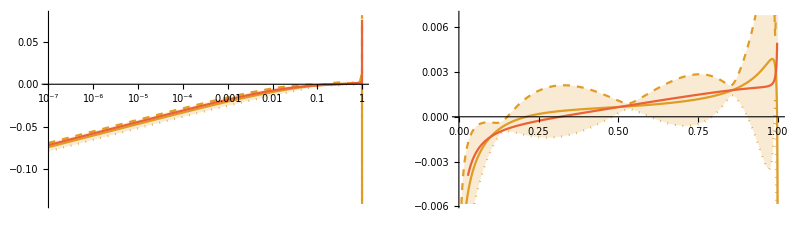

```mathematica
{graphGQcherry, graphGQcherrylog} = PlotErrorBand[ggq2asy,ggq2cherry,4,2];
graphGQExa = Plot[pifact ggq2analyticX /. nf -> 4, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphGQExalog = LogLinearPlot[ pifact ggq2analyticX /. nf -> 4, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
GraphicsRow[{
	Show[graphGQcherrylog, graphGQExalog], 
	Show[graphGQcherry, graphGQExa]
	}, ImageSize -> Full
]
```

### N space Plot

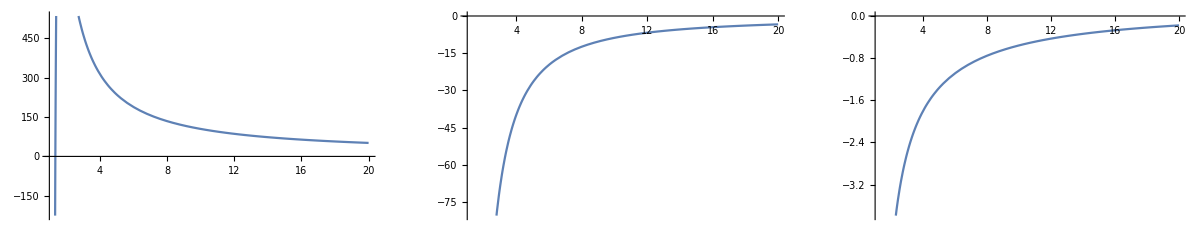

```mathematica
tmp = P2GQN /. N -> n /. {  HarmonicNumber[_] -> S[1, n], HarmonicNumber[n_, a_] -> S[a, n]} /. InverseHarmonicRules;
GraphicsRow[{
	Plot[Coefficient[tmp, NF, 0], {n, 1, 20}],
	Plot[Coefficient[tmp, NF, 1], {n, 1, 20}],
	Plot[Coefficient[tmp, NF, 2], {n, 1, 20}]
}, ImageSize->Full]
```

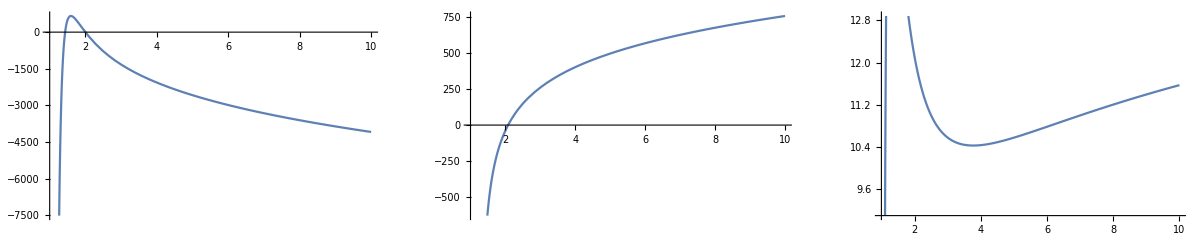

```mathematica
tmp = P2GGN /. N -> n /. {  HarmonicNumber[_] -> S[1, n], HarmonicNumber[n_, a_] -> S[a, n]} /. InverseHarmonicRules;
GraphicsRow[{
	Plot[Coefficient[tmp, NF, 0], {n, 1, 10}],
	Plot[Coefficient[tmp, NF, 1], {n, 1, 10}],
	Plot[Coefficient[tmp, NF, 2], {n, 1, 10}]
}, ImageSize->Full]
```

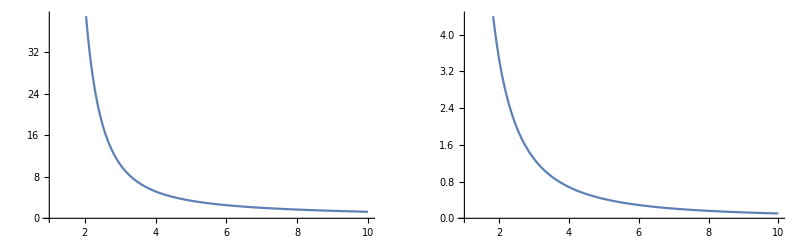

```mathematica
tmp = P2PSN /. N -> n /. {  HarmonicNumber[_] -> S[1, n], HarmonicNumber[n_, a_] -> S[a, n]} /. InverseHarmonicRules;
GraphicsRow[{
	Plot[Coefficient[tmp, NF, 1], {n, 1, 10}],
	Plot[Coefficient[tmp, NF, 2], {n, 1, 10}]
}, ImageSize->Full]
```

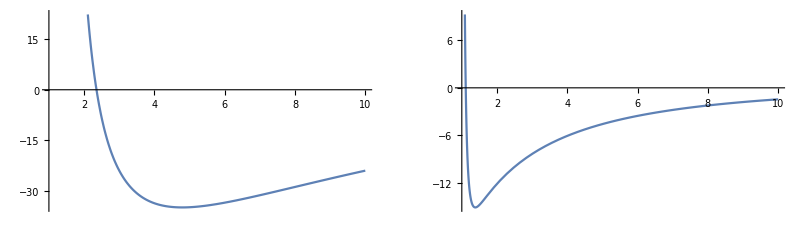

```mathematica
tmp = P2QGN /. N -> n /. {  HarmonicNumber[_] -> S[1, n], HarmonicNumber[n_, a_] -> S[a, n]} /. InverseHarmonicRules;
GraphicsRow[{
  	Plot[Coefficient[tmp, NF, 1], {n, 1, 10}],
  	Plot[Coefficient[tmp, NF, 2], {n, 1, 10}]
  }, ImageSize -> Full]
```

```mathematica
gqq2ps = P2PSN /. N -> n /. {  HarmonicNumber[_] -> S[1, n], HarmonicNumber[n_, a_] -> S[a, n]} ;
gqq2psX =InvMellin[ReduceToBasis[gqq2ps]/. n-> n+1,n,x] /. InvMellinRules  /. hrep//Chop;
```

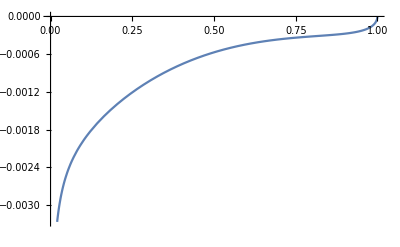

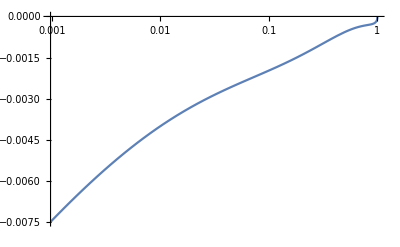

```mathematica
Plot[-x (0.2/(4Pi))^3 gqq2psX/. NF -> 4,{x,0,1} ]
LogLinearPlot[-x (0.2/(4Pi))^3 gqq2psX/. NF -> 4,{x,0,1} ]
```